```mathematica
Clear[a]
par[t_]:=.5*a*t^2+v*t+x
```

```mathematica
Solve[par'[t]==0,t]
```

{{t→-(1. v)/a}}

```mathematica
t0=-v/a;
```

```mathematica
par[t0]
```

-(0.5 v^2)/a+x

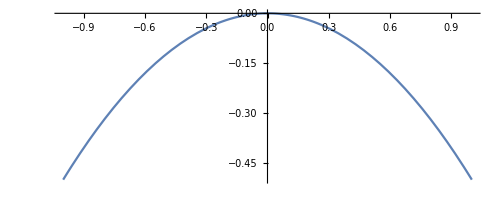

```mathematica
a=1;
ParametricPlot[{-v/a,-.5*v^2/a},{v,-1,1}]
```

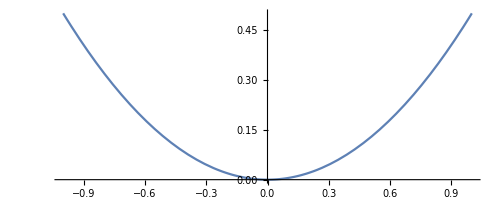

```mathematica
a=-1;
ParametricPlot[{-v/a,-.5*v^2/a},{v,-1,1}]
```